```mathematica
ClearAll["Global`*"];
(*ICs - Initial Conditions *)
ffCartPendulum[ICs_,n_,τ_,τ1_,A_,order_,maxIter_]:=Module[{x,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={xdot,1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),θdot,1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),0,-λ1,2/(A Cos[2 θ]+A-2)^3 (Cos[θ] (4 Sin[θ] (A λ4^2 Cos[2 θ]+4 A λ2^2+(A+2) λ4^2)-(A Cos[2 θ]-3 A+2) (A Cos[2 θ]+A-2) (A θdot^2 λ2-λ4))+A ((A-2) Cos[2 θ]+A) (A Cos[2 θ]+A-2) (λ2-θdot^2 λ4)-4 λ2 λ4 Sin[θ] (3 A Cos[2 θ]+3 A+2)),4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3};
bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];sv=Flatten[Table[{{Subscript[x, i],ICs[[1]]},{Subscript[xdot, i],ICs[[2]]},{Subscript[θ, i],ICs[[3]]},{Subscript[θdot, i],ICs[[4]]},{Subscript[λ1, i],0},{Subscript[λ2, i],0},{Subscript[λ3, i],0},{Subscript[λ4, i],0}},{i,0,n}],1];froot=FindRoot[eqns,sv,MaxIterations->maxIter];
xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];

{xff,xdotff,θff,θdotff,uff}]

testSwingUp[ICs_,τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t,J},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,uff0,J}]

TestSwingUpGeneralFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_] := Piecewise[{{0,0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:=uff[t]+ufb[t];
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{0,0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];
J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]

CalculateGains[xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,i,j,s11,s12,s13,s14,s22,s23,s24,s33,s34,s44,Af,Bf,Q,fx,xState,ric,R,Mf,x2dot,θ2dot},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState];
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S = ({
 {s11, s12, s13, s14},
 {s12, s22, s23, s24},
 {s13, s23, s33, s34},
 {s14, s24, s34, s44}
});
ric =Q +  Afᵀ . S +S . Af -Outer[Times,S . Bf,Bfᵀ . S ] ; (* This is the Syntax for calculating Outer Products *)(*Q = I, M = 0, R = 1*)
RHS = Table[0,{i,4},{j,4}];
x = xff0;xdot = xdotff0;θ =θff0;θdot = θdotff0;u = uff0; (* Entering State Values *)
soltn = NMinimize[{1,ric == RHS},{s11,s12,s13,s14,s22,s23,s24,s33,s34,s44}][[2]];
S = S/.soltn;
K = Bfᵀ . S ;
K]

TestSwingUpGeneralFBNumeric[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,KTable_,n_]:=Module[{K1,K2,K3,K4,eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,ufb,u,θs,θdots,xs,xdots,us,κ1,κ2,κ3,κ4,J},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
K1[t_]:=Piecewise[Table[{KTable[[i]][[1]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],KTable[[n]][[1]]];K2[t_]:=Piecewise[Table[{KTable[[i]][[2]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],KTable[[n]][[2]]];K3[t_]:=Piecewise[Table[{KTable[[i]][[3]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],KTable[[n]][[3]]];K4[t_]:=Piecewise[Table[{KTable[[i]][[4]],(i-1)*τ/n <= t <= i*τ/n},{i,1,n}],KTable[[n]][[4]]];
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_]:=Piecewise[{{K3[t]*(θff[t]-θ[t])+K4[t] *(θdotff[t]-θdot[t])+K1[t]*(xff[t]-x[t])+K2[t] * (xdotff[t]-xdot[t]),0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:=uff[t]+ufb[t];
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{K3[t]*(θff[t]-θs[t])+K4[t] *(θdotff[t]-θdots[t])+K1[t]*(xff[t]-xs[t])+K2[t] * (xdotff[t]-xdots[t]),0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,K1,K2,K3,K4,J}]

simulateLinearFeedbackEnd[ICs_,n_,τ_,τ1_,A_,order_,maxIter_]:= Module[{x1a,xdot1a,θ1a,θdot1a,u1a,
	    x1b,xdot1b,θ1b,θdot1b,u1b,
	    x1c,xdot1c,θ1c,θdot1c,u1c,
      p1a,p1b,p1c,J,J1},

{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter];  
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=TestSwingUpGeneralFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];

p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];

p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];

p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"Linear feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];

{J1,J,p1a,p1b,p1c}]

simulateLQRFeedback[ICs_,n_,n2_,τ_,τ1_,A_]:= Module[{x1a,xdot1a,θ1a,θdot1a,u1a,
	    x1b,xdot1b,θ1b,θdot1b,u1b,
	    x1c,xdot1c,θ1c,θdot1c,u1c,
	    p1a,p1b,p1c,KTable,K1,K2,K3,K4,J},

{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A];
KTable = Table[CalculateGains[x1a[τ1/n2*i],xdot1a[τ1/n2*i],θ1a[τ1/n2*i],θdot1a[τ1/n2*i],u1a[τ1/n2*i],A],{i,0,n2}]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,_}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,K1,K2,K3,K4,J}=TestSwingUpGeneralFBNumeric[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,KTable,n2];

p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];

p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];

p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];

{J,p1a,p1b,p1c}]


CalculateSMatrix[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},

xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState]; (* Fix this *)
Q = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
RHS[t_] := (IdentityMatrix[4] + Afᵀ.S[t] + S[t].Af - KroneckerProduct[S[t].Bf,Bfᵀ.S[t]]) /. {x-> x1a[t], xdot -> xdot1a[t], θ ->θ1a[t], θdot -> θdot1a[t], u -> u1a[t]};
sol2 = S /. NDSolve[{S'[t]== RHS[t],S[0]==S0},S,{t,0,τ }];
S = sol2[[1]]
]
CalculateGains[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,S_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
K = (Bfᵀ.S[τ - time])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]
testWithFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J,S,K},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
S = CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A];
K[t_] := CalculateGains[xff,xdotff,θff,θdotff,uff,t,A,τ,S];
ufb[t_] := Piecewise[{{
K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];u[t_]:=uff[t]+ufb[t];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];
J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]
```

## Understanding Effect of Changing n

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$13251 near {t$13251} = {3.25188}. NIntegrate obtained 35.7232 and 0.000165289 for the integral and error estimates.

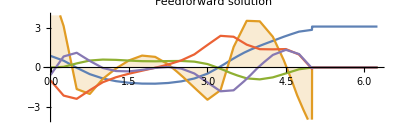

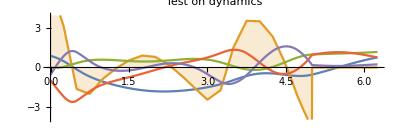

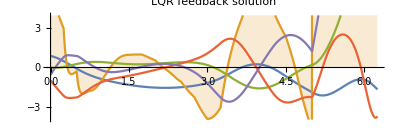

```mathematica
n=20;τ=5;τ1=τ*1.25;A=0.2;order = 1;maxIter = 100;
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit}; (* Random Initialization *)
ICs={0.89486028245609,-0.9468360111172656,-0.002994757534002989,1.677668990900959}; (* Works *)
ICs = {0,-0.5735358669582524,0.8898706763193971,-0.9946572285334812}; (* Doesnt Work *)
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$543645 near {t$543645} = {3.27141}. NIntegrate obtained 62.6641 and 0.000466661 for the integral and error estimates.

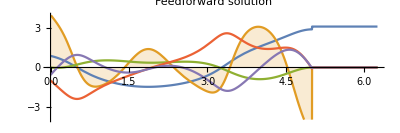

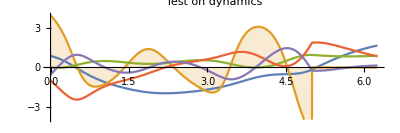

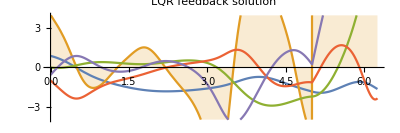

```mathematica
n=234;τ=5;τ1=τ*1.25;A=0.2;order = 1;maxIter = 100;
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit}; (* Random Initialization *)
ICs={0.89486028245609,-0.9468360111172656,-0.002994757534002989,1.677668990900959}; (* Works *)
ICs = {0,-0.5735358669582524,0.8898706763193971,-0.9946572285334812}; (* Doesnt Work *)
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

By Changing n from 234 to 235 we move to a completely new solution!!!

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$584614 near {t$584614} = {3.26164}. NIntegrate obtained 51.5447 and 0.000946889 for the integral and error estimates.

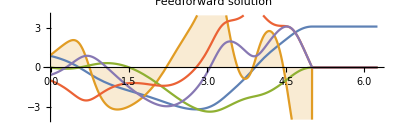

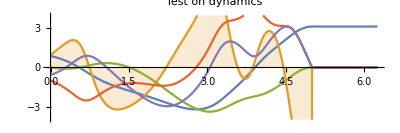

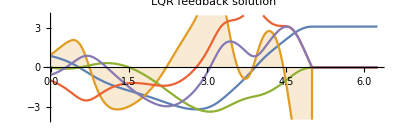

```mathematica
n=235;τ=5;τ1=τ*1.25;A=0.2;order = 1;maxIter = 100; (* Order of Interpolation doesnt matter for such large n*)
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit}; (* Random Initialization *)
ICs={0.89486028245609,-0.9468360111172656,-0.002994757534002989,1.677668990900959}; (* Works *)
ICs = {0,-0.5735358669582524,0.8898706763193971,-0.9946572285334812}; (* Doesnt Work *)
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

Furthermore reducing the max iterations to 20 also works as the feedback corrects the errors

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 20 iterations.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$591587 near {t$591587} = {2.93938}. NIntegrate obtained 48.7701 and 0.00034475 for the integral and error estimates.

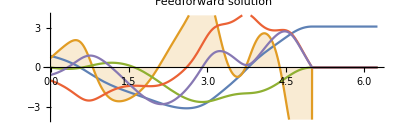

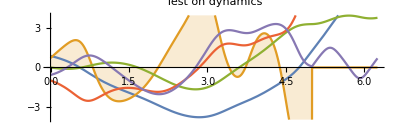

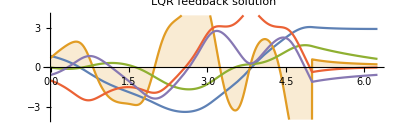

```mathematica
n=235;τ=5;τ1=τ*1.25;A=0.2;order = 1;maxIter = 20; (* Order of Interpolation doesnt matter for such large n*)
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit}; (* Random Initialization *)
ICs={0.89486028245609,-0.9468360111172656,-0.002994757534002989,1.677668990900959}; (* Works *)
ICs = {0,-0.5735358669582524,0.8898706763193971,-0.9946572285334812}; (* Doesnt Work *)
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

Can we come up with a better initial guess that would work for smaller values of n

Try this out by down sampling the true optimal values and using them as initial conditions for smaller values of n

Standard Case

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 40 iterations.

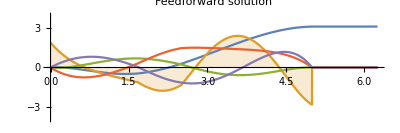

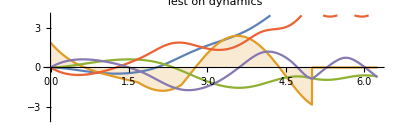

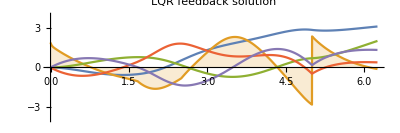

```mathematica
n=6;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 40; (* Order of Interpolation doesnt matter for such large n*)
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit}; (* Random Initialization *)
ICs={0.89486028245609,-0.9468360111172656,-0.002994757534002989,1.677668990900959}; (* Works *)
ICs = {0,-0.5735358669582524,0.8898706763193971,-0.9946572285334812}; (* Doesnt Work *)
ICs = {0,0,0,0};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```